```mathematica
y={-1.48,-1.40, -1.16,-1.08,-1.02,0.14,0.51,0.53,0.078};
```

```mathematica
α=1;
σ1=0.1^2;
θ2=0;
σ2=1;
P["x|θ",{x_,θ1_}]:=PDF[NormalDistribution[θ1,σ1]][x]
P["θ",{θ_}]:=PDF[NormalDistribution[θ2,σ2]][θ]
P["θ|x",{θ_,x_}]=(P["x|θ",{x,θ}]P["θ",{θ}])/(∫_(-∞)^(+∞) P["x|θ",{x,s}]P["θ",{s}]ⅆs)
r[x_]=α∫_(-∞)^(+∞) P["x|θ",{x,θ}]P["θ",{θ}]ⅆθ
ParamUpdate[x_]:=(σ/.Solve[P["θ|x",{x,x}]==PDF[NormalDistribution[x,σ]][x],{σ}])[[1]]
```

39.8962 ⅇ^(0.49995 x^2-5000. (x-θ)^2-θ^2/2)

0.398922 ⅇ^(-0.49995 x^2)

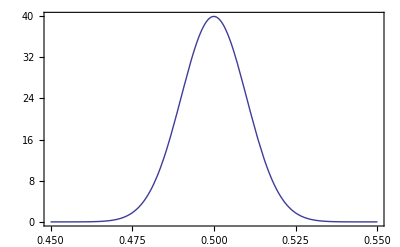

```mathematica
Plot[P["θ|x",{θ,0.5}],{θ,0.45,0.55},PlotRange->All,Frame->True]
```

```mathematica
Sample[x_,θ_,i_]:=Module[{mT,θn,q,b,μ,σ},
θn=Delete[θ,i];
mT=Length[θn];
q=Plus@@Table[P["x|θ",{x[[i]],θn[[j]]}],{j,1,mT}];
b=1/(q+r[x[[i]]]);
μ=x[[i]];
σ=ParamUpdate[μ];
If[Random[]<b q,θ[[RandomInteger[{1,mT}]]],
RandomVariate[NormalDistribution[μ,σ],1][[1]]]]
```

```mathematica
GibbsSampler[x_,n_,m_]:=Module[{N,θ,r},
N=Length[x];
θ=Table[Random[],{N}];
Do[Do[θ[[i]]=Sample[x,θ,i],{i,1,N}],{m}];
r=Table[0,{n},{N}];r[[1]]=θ;
Do[Do[θ[[i]]=Sample[x,θ,i],{i,1,N}];r[[k+1]]=θ,{k,1,n-1}];
r]
```

```mathematica
data=GibbsSampler[y,10,10]
```

{{-1.48955,-1.41069,-1.15791,-1.07743,-1.01559,-1.48955,0.51032,0.51032,0.0853372},{-1.15791,-1.40643,-1.15791,-1.08671,-1.017,0.130271,-1.017,0.526157,0.0752544},{-1.47699,-1.4037,-1.17254,-1.08129,-1.017,0.137189,-1.17254,0.535145,0.0800852},{-1.48851,-1.38237,-1.017,-1.0888,-1.0888,0.143729,-1.48851,0.522088,0.0659139},{-1.017,-1.39917,-1.14981,-1.0888,-1.017,0.145686,-1.48851,0.528345,0.0685327},{-1.39917,-1.39917,-1.1816,-1.07941,-1.01829,0.126963,0.126963,0.525393,0.0719805},{-1.4897,-1.39677,-1.19176,-1.07389,-1.01331,0.126963,-1.01331,0.552751,0.0731902},{-1.49445,-1.3975,-1.1562,-1.08417,0.126963,-1.01331,0.552751,-1.01331,0.0771032},{-1.47479,-1.40825,-1.17591,-1.06469,-1.01331,0.141685,0.50292,-1.17591,0.0906268},{-1.47072,-1.40254,0.141685,-1.08237,-1.02804,-1.08237,0.536962,0.141685,0.0639827}}

```mathematica
density[data_,F_]:=Module[{N},
]
```

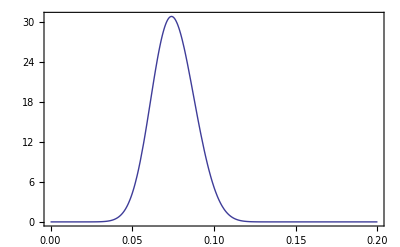

```mathematica
Plot[1/10Plus@@Map[P["x|θ",{x,#}]&,data[[All,-1]]],{x,0,0.2},PlotRange->All,Frame->True]
```

```mathematica
data=GibbsSampler[y,1000,100];
```

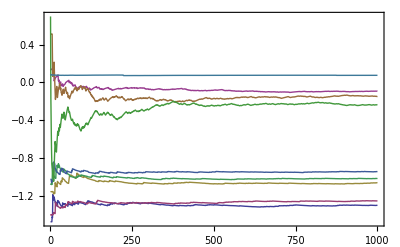

```mathematica
ListPlot[Transpose[data],Frame->True,Joined->True]
```

```mathematica
data=GibbsSampler[y,1000,1000];
```

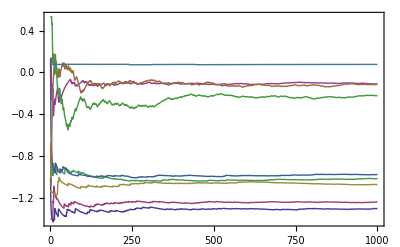

```mathematica
ListPlot[Transpose[data],Frame->True,Joined->True]
```